Taylor approximation (§3.4):

```mathematica
Quit[]
```

```mathematica
f=1/(2-x)
Taylor0=Series[f,{x,1,0}]
Taylor1=Series[f,{x,1,1}]
Taylor2=Series[f,{x,1,2}]
Taylor3=Series[f,{x,1,3}]
```

1/(2-x)

1+O[x-1]^1

1+(x-1)+O[x-1]^2

1+(x-1)+(x-1)^2+O[x-1]^3

1+(x-1)+(x-1)^2+(x-1)^3+O[x-1]^4

```mathematica
linearApprox=Normal[Taylor1]
quadraticApprox=Normal[Taylor2]
cubicApprox=Normal[Taylor3]
```

x

(-1+x)^2+x

(-1+x)^2+(-1+x)^3+x

```mathematica
Expand[cubicApprox]
```

2 x-2 x^2+x^3

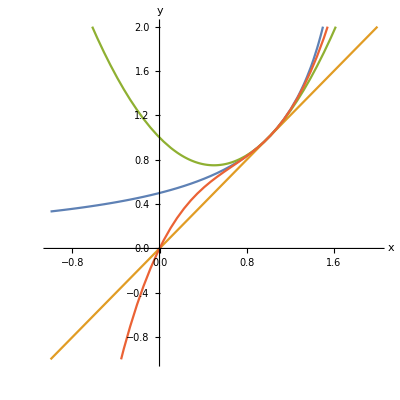

```mathematica
Plot[{f,linearApprox,quadraticApprox,cubicApprox},{x,-1,2},PlotRange->{{-1,2},{-1,2}},AspectRatio->1/1,AxesLabel->{x,y}]
```